This comes from the transfer function given by JOS on his CCRMA website. But the slope looks like 6dB/octave. How is that different from a 1st order butterworth highpass filter?

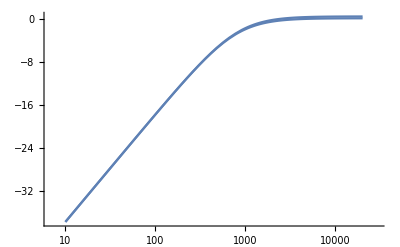

5.82693

```mathematica
dcbl[z_,β_]:=(1-z^(-1))/(1-β z^(-1))
zz[ω_,λ_]:=ⅇ^(ⅈ 2 π ω / λ)
gainToDb[g_]:=20Log10[g]

sr = 48000;
R = 0.9;

Show[
LogLinearPlot[gainToDb[Abs[dcbl[zz[ω,sr],R]]],{ω,10,20000},PlotRange->All],
LogLinearPlot[gainToDb[Abs[dcbl[zz[ω,4sr],1-(1/4)(1-R)]]],{ω,10,20000},PlotRange->All]
]

Manipulate[
LogLinearPlot[gainToDb[Abs[dcbl[zz[ω,sr],1-(c)(1-R)]]],{ω,10,20000},PlotRange->{-40,1}],
{c,0.01,1}]
gainToDb[Abs[dcbl[zz[200,sr],1-(1-R)]]]-gainToDb[Abs[dcbl[zz[100,sr],1-(1-R)]]]
```

## We compare the DC blocker to a first order highpass filter

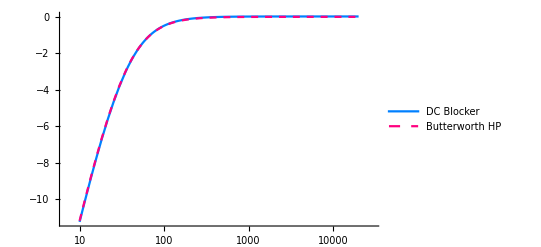

(1/(1.+Tan[(fc π)/48000])-1/(z (1.+Tan[(fc π)/48000])))/(1+(-1.+Tan[(fc π)/48000])/(z (1.+Tan[(fc π)/48000])))

```mathematica
hp6[z_,fc_,sr_]:=Module[{γ,a0,b1,b0,a1},
γ=Tan[π*fc/sr];
a0=(γ+1.0);
b0=1/a0;
b1= -b0;
     a1=(γ-1.0)/a0;

(b0+b1/z)/(1+a1/z)
]
sr= 48000;
Manipulate[
Show[LogLinearPlot[gainToDb[Abs[hp6[zz[ω,sr],fc,sr]]],{ω,10,20000},PlotRange->{-40,1},PlotStyle->Directive[{Hue[7/12]}]],
LogLinearPlot[gainToDb[Abs[dcbl[zz[ω,sr],0.995]]],{ω,10,20000},PlotRange->All, PlotStyle->Directive[{Dashed,Hue[1/12]}]]
],
{{fc,38},20,700}]

highpassFC = 32;
LogLinearPlot[{gainToDb[Abs[dcbl[zz[ω,44100],0.995]]],gainToDb[Abs[hp6[zz[ω,sr],highpassFC,44100]]]},{ω,10,20000},PlotRange->All, PlotStyle->{Hue[7/12],Directive[{Dashed,Hue[11/12]}]},PlotLegends->{"DC Blocker","Butterworth HP"}]
```

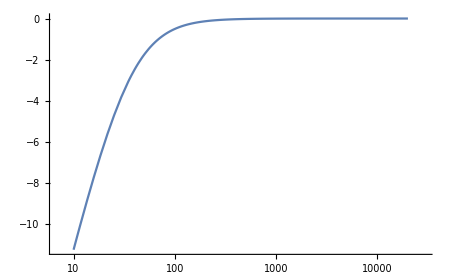

```mathematica
LogLinearPlot[gainToDb[Abs[dcbl[zz[ω,44100],0.995]]],{ω,10,20000},PlotRange->All]
```

```mathematica
fc = 32;
γ=Tan[π*fc/44100];
a0=(γ+1.0);
b0=1/a0;
b1= -b0;
     a1=(γ-1.0)/a0;

(b0+b1 z^(-1))/(1+a1 z^(-1))
```

(0.997726-0.997726/z)/(1-0.995451/z)